Modify these as necessary.

```mathematica
importPath="/Users/jackshi/Desktop/Projects/DeepRobots/Trials/DQN Swimming Trial 15 2019-06-14 12_50_46.841584/policy rollout first 50 steps.csv";
exportPath="/Users/jackshi/Desktop/Projects/DeepRobots/Trials/DQN Swimming Trial 15 2019-06-14 12_50_46.841584/video.avi";
tf=100;
L=2;
xmin=-.6;
xmax=3;
ymin=-3;
ymax=0;
```

```mathematica
numFrames = 1200;
```

Import and set up data.

```mathematica
data=Transpose[Import[importPath]];
x0=ListInterpolation[data[[1]],{{0,tf}}];
y0=ListInterpolation[data[[2]],{{0,tf}}];
th0=ListInterpolation[data[[3]],{{0,tf}}];
a1=ListInterpolation[data[[4]],{{0,tf}}];
a2=ListInterpolation[data[[5]],{{0,tf}}];
```

```mathematica
th1=th0[#]+a1[#]&;
th2=th1[#]+a2[#]&;
x1=x0[#]+L/2 Cos[th0[#]]+L/2 Cos[th1[#]]&;
y1=y0[#]+L/2 Sin[th0[#]]+L/2 Sin[th1[#]]&;
x2=x1[#]+L/2 Cos[th1[#]]+L/2 Cos[th2[#]]&;
y2=y1[#]+L/2 Sin[th1[#]]+L/2 Sin[th2[#]]&;
```

Check the plots to make sure.

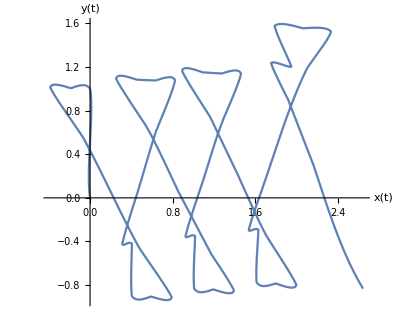

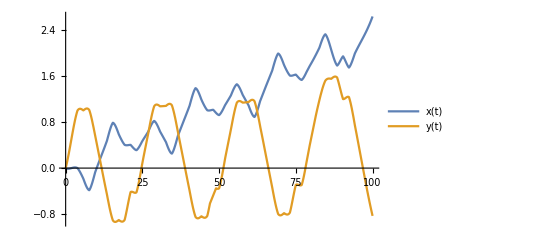

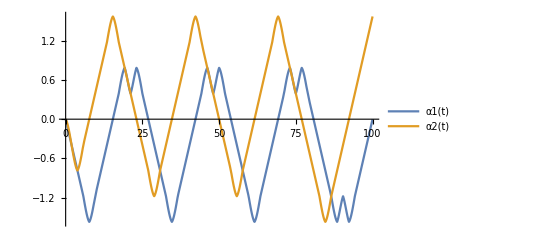

```mathematica
ParametricPlot[{x0[k],y0[k]},{k,0,tf},AxesLabel->{x[t],y[t]}]
Plot[{x0[k],y0[k]},{k,0,tf},PlotLegends->{x[t],y[t]}]
Plot[{a1[k],a2[k]},{k,0,tf},PlotLegends->{α1[t],α2[t]}]
```

Here are some purely aesthetic parameters.

```mathematica
a=1;
b=.25;
```

Here are the elements of a 3 D cartoon.

```mathematica
fluid = Graphics[{RGBColor[0, 0.8, 0.8], Rectangle[{xmin-2L,ymin-2L }, {xmax+2L, ymax+2L}]}, Axes -> True];
link[xCenter_, yCenter_, θ_] = Graphics[{White, EdgeForm[Thick], Rotate[Disk[{xCenter,yCenter}, {a, b}], θ, {xCenter,yCenter}]}];
Show[{link[x1[k],y1[k],th1[k]],link[x2[k],y2[k],th2[k]],link[x0[k],y0[k],th0[k]]}/.k->3.2,Boxed->False]
```

-Graphics-

Animate!

```mathematica
frame[k_] := Show[{fluid, link[x0[k],y0[k],th0[k]], link[x1[k],y1[k],th1[k]], link[x2[k],y2[k],th2[k]]}]
frames = Table[frame[k], {k, 0, tf, tf/numFrames}];
ListAnimate[frames]
```

```mathematica
Export[exportPath,frames];
```